# Mathematica for Bioinformatics

by George I. Mias, PhD
["http://georgemias.org"](http://georgemias.org)

Cite this chapter as:
Mias G. (2018) Metabolomics Example. In: Mathematica for Bioinformatics. Springer, Cham. https://doi.org/10.1007/978-3-319-72377-8_8

## Chapter 8: Metabolomics Example

## Metabolomics Data

## Germ Free and Inoculated Mice Data

The study by Marcobal et al. used two groups of Swiss - Webster germ free (GF) mice (in gnotobiotic isolators). A group of 3 mice was kept germ free, and the second group's gut was colonized with two bacterial species, Bacteroides thetaiotaomicron and Bifidobacterium longum. The data we will use come from an analysis of small molecules from urine collected for the GF mice and at days 5,10,15,20 and 25 from the inoculated mice. The data contain a mass feature (in Dalton) and the intensities for each sample.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
importGFMice=Import["GFMice.csv"];
```

### Processing Imported Data

The imported data contains both Negative and Positive Mode acquired results from mass spectrometry, separated by lines indicating “Negative Mode” and “Positive Mode”. Let us look at the first few lines:

```mathematica
importGFMice[[1;;4]]
```

{{Negative Mode,,,,,,,,,,,,,,,,,,,,,},{mzmed,GF1,GF2,GF3,Day5_BTBL_1,Day5_BTBL_2,Day5_BTBL_3,Day5_BTBL_4,Day10_BTBL_1,Day10_BTBL_2,Day10_BTBL_3,Day10_BTBL_4,Day15_BTBL_1,Day15_BTBL_2,Day15_BTBL_3,Day15_BTBL_4,Day20_BTBL_1,Day20_BTBL_2,Day20_BTBL_3,Day25_BTBL_1,Day25_BTBL_2,Day25_BTBL_3},{,0(GF),0(GF),0(GF),5,5,5,5,10,10,10,10,15,15,15,15,20,20,20,25,25,25},{269.125,4.77187×10^6,1.83739×10^6,2.69081×10^6,1.78109×10^6,1.95988×10^6,1.61111×10^6,1.84043×10^6,3.46027×10^6,7.17564×10^6,4.24283×10^6,5.18863×10^6,3.44216×10^6,5.37601×10^6,5.75372×10^6,5.62317×10^6,5.60079×10^6,4.82033×10^6,2.78184×10^6,2.68937×10^6,3.73472×10^6,5.98949×10^6}}

We can find the location for the positive mode in the file:

```mathematica
positiveModeLocation=Position[importGFMice,"Positive Mode"]
```

{{1559,1}}

We can use Extract directly on the Position output:

```mathematica
Extract[importGFMice,positiveModeLocation]
```

{Positive Mode}

Now we can see if this is correct by looking at data around this position:

```mathematica
importGFMice[[1558;;1559+3]]
```

{{233.097,486634.,236327.,17058.,72046.,66187.,48386.7,100225.,86517.2,174761.,152207.,182583.,194218.,91068.7,185375.,195549.,182746.,173075.,125166.,149478.,156302.,110914.},{Positive Mode,,,,,,,,,,,,,,,,,,,,,},{mzmed,GF1,GF2,GF3,Day5_BTBL_1,Day5_BTBL_2,Day5_BTBL_3,Day5_BTBL_4,Day10_BTBL_1,Day10_BTBL_2,Day10_BTBL_3,Day10_BTBL_4,Day15_BTBL_1,Day15_BTBL_2,Day15_BTBL_3,Day15_BTBL_4,Day20_BTBL_1,Day20_BTBL_2,Day20_BTBL_3,Day25_BTBL_1,Day25_BTBL_2,Day25_BTBL_3},{,GF,GF,GF,5,5,5,5,10,10,10,10,15,15,15,15,20,20,20,25,25,25},{400.148,151323.,111751.,62803.1,37103.3,38007.8,40273.7,62485.1,45894.4,100245.,91827.7,103192.,110570.,64440.1,88330.9,79779.5,90142.1,77907.6,62669.8,51059.6,47668.2,61009.8}}

We can drop all lines we do not want to get the list of all metabolites. The Drop removes lines 1559 to 1561 and the subsequent take ignores the first 3 lines and the first column:

```mathematica
metabolitesGFRawData=Drop[importGFMice,{1559,1561}][[4;;,2;;]];
```

```mathematica
metabolitesGFAnnotations=importGFMice[[1561,2;;]]
```

{GF,GF,GF,5,5,5,5,10,10,10,10,15,15,15,15,20,20,20,25,25,25}

And finally we can obtain the corresponding mass features:

```mathematica
metabolitesGFFeatures=Drop[importGFMice,{1559,1561}][[4;;,1]];
```

```mathematica
metabolitesData=Drop[importGFMice,{1559,1561}][[4;;,2;;]];
```

We will first look at data profiles. We can use SmoothHistogram to plot a smooth kernel histogram of the intensities for each sample. The Transpose gives us the samples as lists. To account for the various ranges we take the Logarithm of the values  x_i (you can pick any base for the logarithm, common bases are 2, 10. occasionally natural log is also used - though natural log is mathematically more intuitive, log base 2 is more convenient when discussing changes in terms of fold changes). We have added 1 to each value, to avoid zero values, which accounts for the secondary peak seen below. This is one method often used to avoid zeros, and in this case the intensities are large so the addition has minimal effect (The data for this accounts for the bump around zero in the histogram figure):

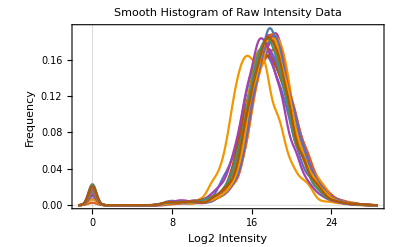

```mathematica
SmoothHistogram[ 
Log2[#+1]&@Transpose[metabolitesData],
PlotRange-> All,PlotTheme->"Scientific",
FrameLabel->{"Log2 Intensity","Frequency"},
PlotLabel->
"Smooth Histogram of Raw Intensity Data"]
```

As an alternative, we will tag 0 values as Missing and delete them:

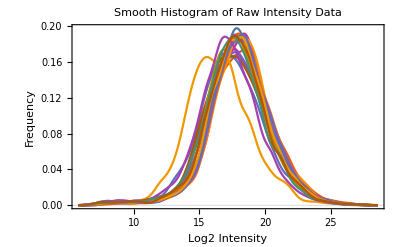

```mathematica
SmoothHistogram[ 
Log2[DeleteMissing[#]+1]&/@
(Transpose[metabolitesData]/. 
0|0.-> Missing[]),PlotRange-> All,
PlotTheme->"Scientific",
FrameLabel->{"Log2 Intensity","Frequency"},
PlotLabel->
"Smooth Histogram of Raw Intensity Data"]
```

The data is not normal, and also we notice that not all means are aligned. We can transform the data in different ways, for example standardize the Log2 values of the data - we use a function from MathIOmica that can handle Missing values (StandardizedExtended), subtracting the mean and dividing by the MeanDeviation:

```mathematica
<<MathIOmica`
```

MathIOmica 1.2.5 (https://mathiomica.org), by [G. Mias Lab](http://georgemias.org)

```mathematica
standardizationLogs=
SeriesApplier[
StandardizeExtended[Log2[#],Mean,MeanDeviation]&,Transpose@metabolitesData/. 0|0.-> Missing[]];
```

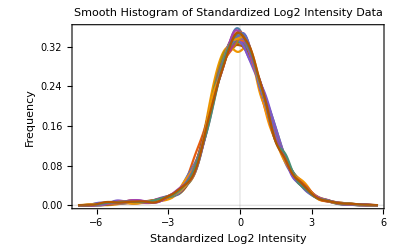

```mathematica
SmoothHistogram[ 
DeleteMissing[#]&/@standardizationLogs,
PlotRange-> All,PlotTheme->"Scientific",
FrameLabel->{"Standardized Log2 Intensity",
"Frequency"},
PlotLabel->
"Smooth Histogram of Standardized Log2 Intensity Data"]
```

Here we perform for the purpose of illustration a power transformation to get the data distributions to be close to normal. The Box-Cox transformation is implemented in MathIOmica:

```mathematica
?ApplyBoxCoxTransform
```

```mathematica
boxCoxTransformedMetaboliteData=ApplyBoxCoxTransform[#]&/@Transpose[metabolitesData/. 0|0.-> Missing[]];
```

Calculated Box-Cox parameter λ̂ = -0.00130934

Calculated Box-Cox parameter λ̂ = 0.0126927

Calculated Box-Cox parameter λ̂ = -0.0109138

Calculated Box-Cox parameter λ̂ = 0.036568

Calculated Box-Cox parameter λ̂ = 0.0434655

Calculated Box-Cox parameter λ̂ = 0.0334664

Calculated Box-Cox parameter λ̂ = 0.0447434

Calculated Box-Cox parameter λ̂ = 0.0312509

Calculated Box-Cox parameter λ̂ = 0.0343907

Calculated Box-Cox parameter λ̂ = 0.0352078

Calculated Box-Cox parameter λ̂ = 0.0268172

Calculated Box-Cox parameter λ̂ = 0.0288383

Calculated Box-Cox parameter λ̂ = 0.0455726

Calculated Box-Cox parameter λ̂ = 0.0485926

Calculated Box-Cox parameter λ̂ = 0.0516518

Calculated Box-Cox parameter λ̂ = 0.037688

Calculated Box-Cox parameter λ̂ = 0.0421872

Calculated Box-Cox parameter λ̂ = 0.0351463

Calculated Box-Cox parameter λ̂ = 0.0305753

Calculated Box-Cox parameter λ̂ = 0.0403079

Calculated Box-Cox parameter λ̂ = 0.0406148

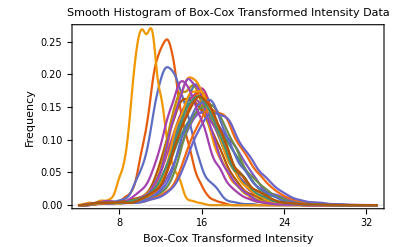

```mathematica
SmoothHistogram[ 
DeleteMissing[#]&/@
boxCoxTransformedMetaboliteData,PlotRange-> All,
PlotTheme->"Scientific",
FrameLabel->{"Box-Cox Transformed Intensity",
"Frequency"},
PlotLabel->
"Smooth Histogram of Box-Cox Transformed Intensity Data"]
```

```mathematica
standardizedMetaboliteData= StandardizeExtended[#,Mean,StandardDeviation]&/@boxCoxTransformedMetaboliteData;
```

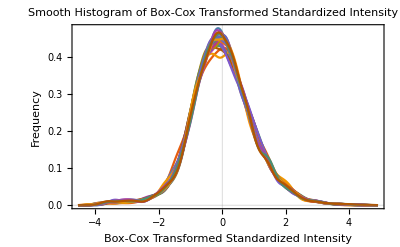

```mathematica
SmoothHistogram[ 
DeleteMissing[#]&/@standardizedMetaboliteData,
PlotRange-> All,PlotTheme->"Scientific",
FrameLabel->
{"Box-Cox Transformed Standardized Intensity",
"Frequency"},
PlotLabel->
"Smooth Histogram of Box-Cox Transformed Standardized Intensity Data"]
```

## Principal Component Analysis

```mathematica
principalComponentsMetabolites=PrincipalComponents[standardizedMetaboliteData/._Missing-> 0,Method->"Correlation"];
```

```mathematica
Dimensions[principalComponentsMetabolites]
```

{21,3247}

```mathematica
varianceRatios=Variance[principalComponentsMetabolites]/Plus@@Variance[principalComponentsMetabolites];
```

```mathematica
varianceRatios[[1;;5]]
```

{0.374437,0.26746,0.097374,0.0624436,0.0412076}

```mathematica
positionsGFAnnotations=Thread[{Range[Length[metabolitesGFAnnotations]],metabolitesGFAnnotations}]
```

{{1,GF},{2,GF},{3,GF},{4,5},{5,5},{6,5},{7,5},{8,10},{9,10},{10,10},{11,10},{12,15},{13,15},{14,15},{15,15},{16,20},{17,20},{18,20},{19,25},{20,25},{21,25}}

```mathematica
groupsGFAnnotations=GroupBy[positionsGFAnnotations,Last-> First]
```

<|GF→{1,2,3},5→{4,5,6,7},10→{8,9,10,11},15→{12,13,14,15},20→{16,17,18},25→{19,20,21}|>

```mathematica
ListPointPlot3D[
principalComponentsMetabolites[[All,
{1,2,3}]][[#]]&/@
(Values@groupsGFAnnotations),
PlotStyle->({#,PointSize[0.025]}&/@#),
PlotLegends-> 
SwatchLegend[#,
Style[#,FontFamily->"Arial"]&/@{"GF","5 Days","10 Days","15 Days","20 Days","25 Days"},
LegendLabel->Style["Mouse Groups",Italic,
FontFamily->"Arial"],
LegendMarkers->"Bubble"],
PlotLabel->
Style[
"Principal Component Analysis of Normalized Feature Data",
Bold,FontFamily->"Arial"],
AxesLabel-> {"P1","P2","P3"}]&@
{Green,Blue,Cyan,Red,Orange,Purple}
```

-Graphics3D-

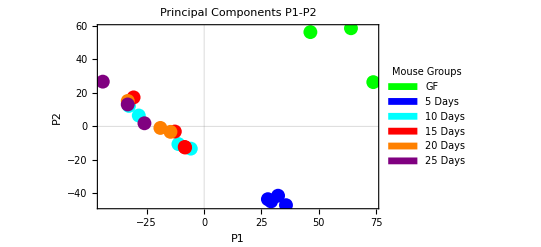

```mathematica
ListPlot[
principalComponentsMetabolites[[All,
{1,2}]][[#]]&/@
(Values@groupsGFAnnotations),
PlotStyle->({#,PointSize[0.025]}&/@#),
PlotLegends-> 
SwatchLegend[#,
Style[#,FontFamily->"Arial"]&/@
{"GF","5 Days","10 Days","15 Days",
"20 Days","25 Days"},
LegendLabel->Style["Mouse Groups",Italic,
FontFamily->"Arial"],
LegendMarkers->"Bubble"],
PlotLabel->Style["Principal Components P1-P2",
Bold,FontFamily->"Arial"],
FrameLabel-> {"P1","P2"},
PlotRange->All,
PlotTheme->"Scientific"]&@
{Green,Blue,Cyan,Red,Orange,Purple}
```

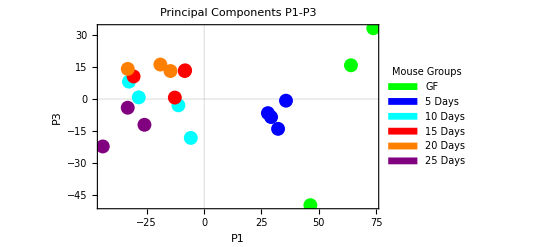

```mathematica
ListPlot[
principalComponentsMetabolites[[All,
{1,3}]][[#]]&/@
(Values@groupsGFAnnotations),
PlotStyle->({#,PointSize[0.025]}&/@#),
PlotLegends-> 
SwatchLegend[#,
Style[#,FontFamily->"Arial"]&/@
{"GF","5 Days","10 Days","15 Days",
"20 Days","25 Days"},
LegendLabel->Style["Mouse Groups",Italic,
FontFamily->"Arial"],
LegendMarkers->"Bubble"],
PlotLabel->Style["Principal Components P1-P3",
Bold,FontFamily->"Arial"],
FrameLabel-> {"P1","P3"},
PlotRange->All,
PlotTheme->"Scientific"]&@
{Green,Blue,Cyan,Red,Orange,Purple}
```

## Differential Analysis GF vs 5 Days After Inoculation

We have seen from the PCA analysis that GF mice have a different overall urine metabolome profile. We will investigate this further in this section, to show how we can carry out differential metabolite analysis for GF vs Day5 mice. First we get the relevant data, the first 7 columns, with columns 1-3 corresponding to the GF mice, and columns 4-7 corresponding to D5 mice. We transpose the sets so that the features are in rows, and create a feature to data association using AssociationThread:

```mathematica
gfD5Micedata=AssociationThread[metabolitesGFFeatures,{#[[1;;3]],#[[4;;7]]}&/@Transpose @standardizedMetaboliteData];
```

```mathematica
gfD5Micedata[[1;;3]]
```

<|269.125→{{1.59827,1.3155,1.9353},{1.20028,1.23387,1.18128,1.10904}},225.083→{{0.513168,0.734814,1.04897},{0.626587,0.702056,0.671343,0.689867}},323.134→{{0.320948,0.200707,0.51853},{0.275585,0.254827,0.257726,0.419021}}|>

```mathematica
Length[gfD5Micedata]
```

3247

Some data can have Missing values. In our analysis here we want to remove data that have less than 3 numeric values. In each value in our association we have a list for GF mice, and one for Day 5.  For GF mice we have 3 data points.   Additionally, we could be missing data in the Day 5 features. For the second list in each value (the Day 5 intensities for a given feature) we have 4 points.  We can remove data that have less than or equal to 2 points in either list after we delete Missing data. First we can delete all missing values:

```mathematica
Query[All,All,DeleteMissing]@gfD5Micedata;
```

```mathematica
filteredGFd5Data=Query[Select[ (Length[#[[1]]]==3)&&Length[#[[2]]]≥  3&]]@(Query[All,All,DeleteMissing]@gfD5Micedata);
```

```mathematica
Length[filteredGFd5Data]
```

3175

This corresponds to dropping 72 data points compared to the original .

We will apply a location test to each small metabolite using LocationTest (see also Chapter 3 and 6 for gene expression data). For example:

```mathematica
LocationTest[filteredGFd5Data[[1]],Automatic,{"TestDataTable",{"MannWhitney","T","Z"}}]
```

| Statistic | P-Value
Mann-Whitney | 12. | 0.0215563
T | 2.40355 | 0.132893
Z | 2.40355 | 0.0162366

```mathematica
LocationTest[filteredGFd5Data[[1]],Automatic,"TestConclusion"]
```

The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the T test.

```mathematica
testGFd5Conclusions=Query[All,LocationTest[#,Automatic,{"PValue","ShortTestConclusion"}]&]@filteredGFd5Data;
```

```mathematica
testGFd5Conclusions[[1;;3]]
```

<|269.125→{0.132893,Do not reject},225.083→{0.610388,Do not reject},323.134→{0.640274,Do not reject}|>

```mathematica
Length[#]&/@GroupBy[testGFd5Conclusions,Last]
```

<|Do not reject→1724,Reject→1451|>

We are testing many hypotheses, so we have to correct for that. Using a Bonferroni correction we can set the p value cutoff at at 0.05/3175 (i.e. divide 0.05 significance cutoff by the number of tests cf. Chapter 6):

```mathematica
testGFd5ConclusionsBFCorrected=Query[All,LocationTest[#,Automatic,{"PValue","ShortTestConclusion"},SignificanceLevel->(0.05/3175)]&]@filteredGFd5Data;
```

In this approach  87 results are listed as rejecting the null hypothesis:

```mathematica
Length[#]&/@GroupBy[testGFd5ConclusionsBFCorrected,Last]
```

<|Do not reject→3088,Reject→87|>

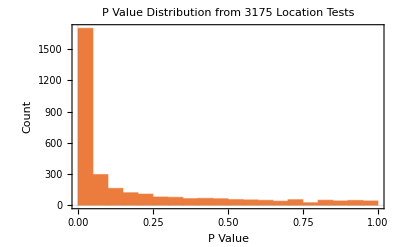

```mathematica
Histogram[testGFd5ConclusionsBFCorrected[[All,1]],
PlotTheme->"Scientific",
PlotLabel->
"P Value Distribution from 3175 Location Tests",
FrameLabel-> {"P Value", "Count"}]
```

Based on the plot, we may think that the Bonferroni correction is a bit strict. We now use the Benjamini-Hochberg False Discovery Rate (FDR) correction instead:

```mathematica
testGFd5FDRResults=BenjaminiHochbergFDR[Values@testGFd5ConclusionsBFCorrected[[All,1]],SignificanceLevel-> 0.05];
```

```mathematica
Keys@testGFd5FDRResults
```

{Results,p-Value Cutoff,q-Value Cutoff}

```mathematica
Query["Results",1;;5]@testGFd5FDRResults
```

{{0.0361271,0.0723224,False},{0.510254,0.59083,False},{0.640274,0.70732,False},{0.00260507,0.0106799,True},{0.137148,0.204915,False}}

```mathematica
testGFd5FDRResults["p-Value Cutoff"]
```

0.0217436

```mathematica
testGFd5FDRResults["q-Value Cutoff"]
```

0.0497377

```mathematica
pValuesGFd5FDR=Query["Results",(AssociationThread[Keys[testGFd5ConclusionsBFCorrected]-> #]&)]@testGFd5FDRResults;
pValuesGFd5FDR//Short[#,4]&
```

<|269.125→{0.0361271,0.0723224,False},«3173»,235.178→{0.418964,0.505976,False}|>

```mathematica
significantQuery=Query[Select[#[[3]]==True&]]@pValuesGFd5FDR;
```

```mathematica
significantQuery[[1;;3]]
```

<|86.0247→{0.00260507,0.0106799,True},301.056→{0.00411965,0.0145214,True},130.039→{0.000253831,0.00220311,True}|>

```mathematica
Length[significantQuery]
```

1388

We can extract the values and also calculate an effect size for all these values. As we have already transformed the data to normal distributions, we look at the shift of the data means as an effective fold size:

```mathematica
deltaGFd5Data=Query[All,Mean[#[[2]]]-Mean[#[[1]]]&]@filteredGFd5Data;
```

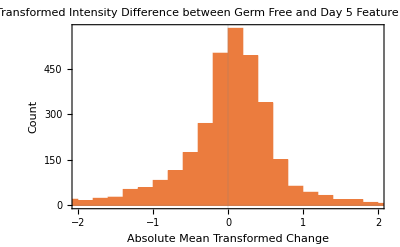

```mathematica
Histogram[deltaGFd5Data,
PlotTheme->"Scientific",
PlotLabel->
"Transformed Intensity Difference between
 Germ Free and Day 5 Feature Intensities",
FrameLabel->{"Absolute Mean Transformed Change",
"Count"}]
```

```mathematica
pValueNegLogGFd5Data= -Log10@Query[All,2]@pValuesGFd5FDR;
```

```mathematica
volcanoPlotGFd5Data=Merge[{deltaGFd5Data,pValueNegLogGFd5Data},Identity];
```

Now we can construct a volcano plot, with  reference lines corresponding to cutoffs, typically at +/- 1 for transformed mean change, and also at -Log10[0.05] for significance (see also Chapter 6).

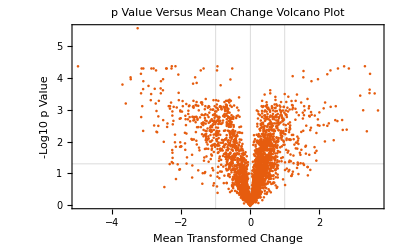

```mathematica
ListPlot[Values@volcanoPlotGFd5Data,
PlotTheme-> "Scientific",
PlotRange-> Full,
PlotLabel-> 
"p Value Versus Mean Change Volcano Plot",
FrameLabel->{"Mean Transformed Change", "-Log10 p Value"},
GridLines->
{{{-1,{Red,Thick,Dashed}},0,
{1,{Red,Thick,Dashed}}},
{{-Log10[0.05],{Blue,Thick,Dashed}}}}]
```

```mathematica
selectedFeaturesGFd5=Query[Select[Abs[#[[1]]]>1&& #[[2]]> (-Log10[0.05])&]]@volcanoPlotGFd5Data;
```

```mathematica
Length[selectedFeaturesGFd5]
```

366

```mathematica
selectedFeaturesGFd5[[1;;10]]
```

<|238.045→{-1.65905,3.09779},338.146→{2.71869,4.37504},388.136→{-2.3985,2.57451},279.038→{-1.88966,1.9473},128.028→{-1.35472,2.17012},178.983→{-1.43019,2.45974},420.109→{-2.2604,1.73732},128.034→{-1.3964,2.23483},353.085→{-2.00294,1.85289},178.034→{-1.21014,2.1053}|>

## Identifying Compounds Using ChemSpider

Here we show how can use the Wolfram Language to connect to the ChemSpider API. There is an inbuilt service to access ChemSpider database information, and we will use it to match our mass features

```mathematica
chemSpider=ServiceConnect["ChemSpider"]
```

ServiceObject[…]

```mathematica
(* May need to run as "New" to create/register for new API key [uncomment and run the command below]*)
```

```mathematica
(*chemSpider=ServiceConnect["ChemSpider","New"] *)
```

```mathematica
chemSpiderDatabases=chemSpider["Databases"];
```

```mathematica
chemSpiderDatabases//Short
```

{abcr,«275»,Yeast Metabolome Database}

Can choose from many databases. In this example we search NIST and ChEMBL. N.B. The “Databases” specification is required to search by mass. Up to 20 databases can be specified.

```mathematica
idExample=chemSpider["Search","Databases"->{"NIST","ChEMBL"},
"Mass"-> 238.0452933,"Range"->0.001,MaxItems->15]
```

```mathematica
Normal@idExample
```

{<|ID→76736296|>,<|ID→484487|>,<|ID→9022829|>,<|ID→9737965|>,<|ID→21667534|>,<|ID→10006113|>,<|ID→71899|>,<|ID→63109|>}

```mathematica
id63109Info=chemSpider["CompoundInformation",
"ID"->"63109"]
```

```mathematica
Head[id63109Info]
```

Dataset

```mathematica
Normal@id63109Info
```

<|ID→63109,SMILES→c1ccc(cc1)c2cc(=O)c3ccccc3s2,Formula→C_{15}H_{10}OS,AverageMass→238.304 Da,MolecularWeight→238.304,MonoisotopicMass→238.045 Da,NominalMass→238 Da,CommonName→Thioflavone,ReferenceCount→60,DataSourceCount→42,PubMedCount→1,RSCCount→2,MOL2D→{Molecule[…]},MOL3D→{Molecule[…]},InChI→InChI=1/C15H10OS/c16-13-10-15(11-6-2-1-3-7-11)17-14-9-5-4-8-12(13)14/h1-10H,InChIKey→GIQPSSZMIZARDW-UHFFFAOYAA,StdInChI→InChI=1S/C15H10OS/c16-13-10-15(11-6-2-1-3-7-11)17-14-9-5-4-8-12(13)14/h1-10H,StdInChIKey→GIQPSSZMIZARDW-UHFFFAOYSA-N|>

N.B. Extended compound information is now provided by “CompoundInformation”

```mathematica
chemSpider["CompoundThumbnail","ID"-> "63109"]
```

-Graphics-

```mathematica
Normal@chemSpider["Search","Query"->"2-Phenyl-4H-thiochromen-4-one"]
```

{<|ID→63109|>}

```mathematica
resultsIDs=chemSpider["Search","Mass"-> #,"Range"->(5*10^(-6)*#),MaxItems->5,"Databases"->{"NIST","ChEMBL"}]&/@(Keys@selectedFeaturesGFd5);
```

```mathematica
Tally[Length[#]&/@resultsIDs]
```

{{5,233},{0,83},{1,24},{2,9},{4,10},{3,7}}

We notice that 259 IDs are not unique (2+ items each, up to 5, which is the maximum in the request), 24 are unique and 83 have no matches. We are interested in the unique ones, so let us extract them:

```mathematica
positionsChemSpiderUnique=Position[resultsIDs,x_/;Length[x]==1]
```

{{10},{40},{46},{54},{57},{91},{106},{114},{133},{144},{148},{149},{175},{178},{179},{200},{203},{261},{284},{286},{288},{299},{310},{321}}

```mathematica
chemSpiderUniqueIDs=#[[1]]&/@Query[(Select[Length[#]==1&]),1]@resultsIDs
```

{73419,512505,120057,66462,56423,13188546,25043329,4921993,76808798,34221265,31125602,42861,2050613,513115,494200,522705,23107776,29419789,23136140,71333,29729378,5037,4932341,26342698}

NB #[[1]] above extracts the value from the results

```mathematica
featuresGFd5ChemSpiderID=AssociationThread[Extract[Keys@selectedFeaturesGFd5,positionsChemSpiderUnique],chemSpiderUniqueIDs]
```

<|178.034→73419,180.979→512505,106.998→120057,220.976→66462,177.006→56423,260.15→13188546,128.107→25043329,171.006→4921993,228.124→76808798,142.068→34221265,289.997→31125602,150.019→42861,195.913→2050613,305.872→513115,307.87→494200,178.053→522705,134.035→23107776,235.13→29419789,170.98→23136140,167.926→71333,347.215→29729378,175.115→5037,218.175→4932341,261.18→26342698|>

```mathematica
chemSpider["CompoundInformation","ID"->76808798]
```

Import::fmterr: Cannot import data as SDF format.

```mathematica
featuresGFd5ChemSpiderIDExtended=Query[All,Normal@chemSpider["CompoundInformation","ID"->#]&,FailureAction-> None]@featuresGFd5ChemSpiderID;
```

Import::fmterr: Cannot import data as SDF format.

N.B. Above, some data raises exceptions - Setting FailureAction -> None allows the computation to proceed.

```mathematica
Query[1,Keys]@featuresGFd5ChemSpiderIDExtended
```

{ID,SMILES,Formula,AverageMass,MolecularWeight,MonoisotopicMass,NominalMass,CommonName,ReferenceCount,DataSourceCount,PubMedCount,RSCCount,MOL2D,MOL3D,InChI,InChIKey,StdInChI,StdInChIKey}

```mathematica
Query[All,"CommonName"]@featuresGFd5ChemSpiderIDExtended
```

<|178.034→1,2-Ethanediyl dicarbamimidothioate,180.979→3-[2-Chloroethyl]-2-thiazolidinethione,106.998→Acrylonitrile, trifluoro-,220.976→METHYL 3-AMINO-5,6-DICHLORO-2-PYRAZINECARBOXYLATE,177.006→Beryllium sulfate hydrate (1:1:4),260.15→3-(1-Piperidinylmethyl)pyrimido[5,4-e][1,2,4]triazine-5,7-diamine,128.107→1-Cyclopropyl-1-(2-hydroxyethyl)aziridinium,171.006→5-(4-chloro-1H-1,2,3-triazol-5-yl)-1H-tetrazole,228.124→3-(1H-Benzotriazol-1-ylmethyl)-1,2-dimethyl-1H-imidazol-3-ium,142.068→5-Ethyl-3,4-dimethyl-1,3-thiazol-3-ium,289.997→(2Z)-3-(4-Fluorophenyl)-2-[(Z)-(4-oxo-2-thioxo-1,3-thiazolidin-5-ylidene)methyl]acrylonitrile,150.019→N-(2-Chloroethyl)-N-nitrosoacetamide,195.913→2,2,2-Trichloroethanimidamide hydrochloride (1:1),305.872→[(2,2-Dibromocyclopropyl)sulfanyl]benzene,307.87→7-Bromo-8-iodobicyclo[4.2.0]octa-1,3,5-triene,178.053→2574929,134.035→Sodium [(1R)-2-methylenecyclopropyl]acetate,235.13→1-[2-Amino-9-(2-aminoethyl)-9H-purin-6-yl]guanidine,170.98→3-Amino-1-propaneseleninic acid,167.926→1812106,347.215→1-(4-Ethyl-5-{1-[(5-methyl-2-thienyl)methyl]-4-piperidinyl}-4H-1,2,4-triazol-3-yl)-N,N-dimethylmethanamine,175.115→SKF-91488,218.175→4-Butoxy-2-hydroxy-N,N,N-trimethyl-4-oxo-1-butanaminium,261.18→4-{[2-(2-Methoxyethoxy)ethoxy]carbonyl}-1,1-dimethylpiperazin-1-ium|>

```mathematica
Query[All,"ID"]@featuresGFd5ChemSpiderIDExtended
```

<|178.034→73419,180.979→512505,106.998→120057,220.976→66462,177.006→56423,260.15→13188546,128.107→25043329,171.006→4921993,228.124→76808798,142.068→34221265,289.997→31125602,150.019→42861,195.913→2050613,305.872→513115,307.87→494200,178.053→522705,134.035→23107776,235.13→29419789,170.98→23136140,167.926→71333,347.215→29729378,175.115→5037,218.175→4932341,261.18→26342698|>

```mathematica
Query[{7},"SMILES"]@featuresGFd5ChemSpiderIDExtended
```

<|128.107→C1CC1[N+]2(CC2)CCO|>

We can extract all the MOL directly :

```mathematica
chemSpiderIDMOL=Query[1;;3,"MOL2D"]@featuresGFd5ChemSpiderIDExtended
```

<|178.034→{Molecule[…]},180.979→{Molecule[…]},106.998→{Molecule[…]}|>

```mathematica
Query[1,1]@
chemSpiderIDMOL
```

Molecule[…]

We can plot the molecules directly:

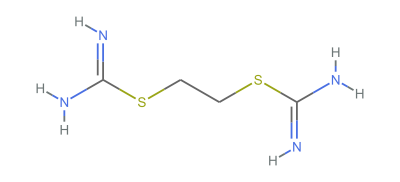
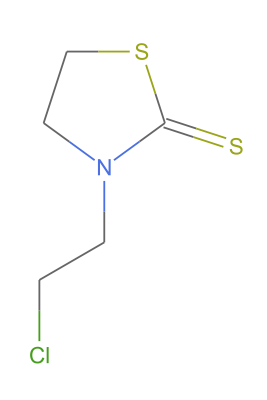
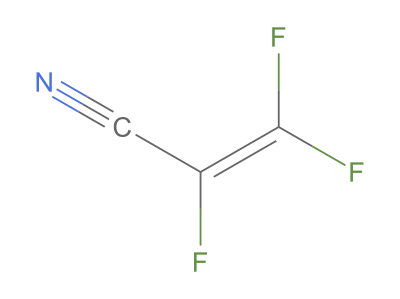
<|178.034→-Graphics-,180.979→-Graphics-,106.998→-Graphics-|>

```mathematica
Query[1;;3,"MOL2D",1/*MoleculePlot]@featuresGFd5ChemSpiderIDExtended
```

```mathematica
ServiceDisconnect[chemSpider]
```

## Identifying Compounds and Pathway Analysis: KEGG

```mathematica
putativeIDs=MassMatcher[#,3]&/@Keys@selectedFeaturesGFd5;
```

```mathematica
putativeIDs//Short
```

{{},{},«362»,{},{}}

```mathematica
Tally[putativeIDs]
```

{{{},346},{{cpd:C01852,cpd:C09781,cpd:C09802},1},{{cpd:C18409},1},{{cpd:C16698,cpd:C19770,cpd:C21027},1},{{cpd:C18922},1},{{cpd:C08503,cpd:C14538},1},{{cpd:C05983},1},{{cpd:C09123},1},{{cpd:C18421},1},{{cpd:C14648},1},{{cpd:C18553},1},{{cpd:C06862},1},{{cpd:C17132,cpd:C17133,cpd:C17136},1},{{cpd:C05366,cpd:C08831,cpd:C09077,cpd:C09515,cpd:C09516,cpd:C10317,cpd:C10558,cpd:C10682,cpd:C17414,cpd:C17508,cpd:C17808,cpd:C20455},1},{{cpd:C00062,cpd:C00792,cpd:C02385},1},{{cpd:C10545,cpd:C10563,cpd:C10640},1},{{cpd:C09098},1},{{cpd:C17704},1},{{cpd:C15193,cpd:C18927},1},{{cpd:C17364},1},{{cpd:C15660},1}}

```mathematica
ppm10putativeIDs=MassMatcher[#,10]&/@Keys@selectedFeaturesGFd5;
```

```mathematica
ppm10putativeIDs[[1;;45]]
```

{{},{cpd:C19333},{cpd:C01852,cpd:C04541,cpd:C09781,cpd:C09802},{},{cpd:C16472,cpd:C16473},{},{},{cpd:C08734},{cpd:C18592},{},{},{},{},{},{},{},{},{},{},{},{},{cpd:C08477,cpd:C10583},{},{},{},{},{cpd:C20313},{},{cpd:C08549},{},{},{},{},{},{},{cpd:C18409},{},{},{},{},{},{},{},{},{}}

```mathematica
positionsPutativeIDs=Position[putativeIDs,x_/;Length[x]==1]
```

{{36},{75},{161},{181},{186},{187},{206},{230},{314},{346},{360},{364}}

```mathematica
selectedFeaturesGFd5[[{360}]]
```

<|315.144→{1.91576,2.275}|>

```mathematica
accessionPutativeIDs=Flatten@Extract[putativeIDs,positionsPutativeIDs]
```

{cpd:C18409,cpd:C18922,cpd:C05983,cpd:C09123,cpd:C18421,cpd:C14648,cpd:C18553,cpd:C06862,cpd:C09098,cpd:C17704,cpd:C17364,cpd:C15660}

```mathematica
compoundDictionary=KEGGDictionary[KEGGQuery1-> "cpd",KEGGQuery2-> ""];
```

```mathematica
compoundDictionary[[1;;10]]
```

<|cpd:C00001→H2O; Water,cpd:C00002→ATP; Adenosine 5'-triphosphate,cpd:C00003→NAD+; NAD; Nicotinamide adenine dinucleotide; DPN; Diphosphopyridine nucleotide; Nadide; beta-NAD+,cpd:C00004→NADH; DPNH; Reduced nicotinamide adenine dinucleotide,cpd:C00005→NADPH; TPNH; Reduced nicotinamide adenine dinucleotide phosphate,cpd:C00006→NADP+; NADP; Nicotinamide adenine dinucleotide phosphate; beta-Nicotinamide adenine dinucleotide phosphate; TPN; Triphosphopyridine nucleotide; beta-NADP+,cpd:C00007→Oxygen; O2,cpd:C00008→ADP; Adenosine 5'-diphosphate,cpd:C00009→Orthophosphate; Phosphate; Phosphoric acid; Orthophosphoric acid,cpd:C00010→CoA; Coenzyme A; CoA-SH|>

```mathematica
Query[accessionPutativeIDs]@compoundDictionary
```

<|cpd:C18409→Cycloprothrin,cpd:C18922→Dinocton 6,cpd:C05983→Propionyladenylate; Propionyl-adenosine monophosphate,cpd:C09123→Athamantin,cpd:C18421→Propamocarb hydrochloride,cpd:C14648→6alpha-Chloro-17-acetoxyprogesterone; 6alpha-Chloro-17-hydroxypregn-4-ene-3,20-dione acetate,cpd:C18553→Spirodiclofen,cpd:C06862→Busulfan,cpd:C09098→Canthin-6-one; 6H-Indolo(3,2,1-de)(1,5)naphthyridin-6-one,cpd:C17704→Antibiotic JI-20A; JI-20A,cpd:C17364→Clavamycin D,cpd:C15660→A 77003|>

```mathematica
Entity["Chemical","Busulfan"]
```

busulfan

```mathematica
Entity["Chemical","Busulfan"]
```

busulfan

```mathematica
CanonicalName[#]&/@Entity["Chemical"]["Properties"]
```

{AcidityConstants,AdjacencyMatrix,AlternateNames,AromaticAtomCount,AromaticQ,AtomCount,AtomPositions,AutoignitionPoint,BeilsteinNumber,BlackStructureDiagram,BoilingPoint,BondCounts,BondEnergies,BondLengths,CASNumber,CHBlackStructureDiagram,CHColorStructureDiagram,ChemicalHybridization,CIDNumber,Codons,ColorStructureDiagram,CombustionHeat,CriticalPressure,CriticalTemperature,Density,DielectricConstant,DipoleMoment,DOTHazardClass,DOTNumbers,DrugInteractions,EdgeRules,EdgeTypes,EGECNumber,ElectronAffinity,ElectronCount,ElementCounts,ElementMassFraction,ElementTypes,EntityClasses,EUNumber,FlashPoint,FormalCharges,FormattedName,Formula,FormulaString,FusionHeat,GmelinNumber,HBondAcceptorCount,HBondDonorCount,HenryLawConstant,HildebrandSolubility,HillFormula,HillFormulaString,InChI,IonCounts,IonEquivalents,Ions,IsoelectricPoint,IsomericSMILES,Isomers,IUPACName,LewisDotStructureDiagram,LightSpeed,LogAcidityConstants,LowerExplosiveLimit,MDLNumber,MeanFreePath,MeltingPoint,Memberships,MolarMass,MolarVolume,MolecularMass,MoleculePlot,Name,NetCharge,NFPAFireRating,NFPAHazards,NFPAHealthRating,NFPALabel,NFPAReactivityRating,NonHydrogenCount,NonStandardIsotopeCount,NonStandardIsotopeCounts,NonStandardIsotopeNumbers,NSCNumber,OdorThreshold,OdorType,OxidationStates,PartitionCoefficient,pH,Phase,ProtonAffinity,ProtonCount,RefractiveIndex,RelativeMolecularMass,Resistivity,RotatableBondCount,RTECSClasses,RTECSNumber,SideChainLogAcidityConstant,SMILES,Solubility,SpaceFillingMoleculePlot,StickMoleculePlot,SurfaceTension,TautomerCount,ThermalConductivity,TopologicalPolarSurfaceArea,UpperExplosiveLimit,VanDerWaalsConstants,VaporDensity,VaporizationHeat,VaporPressure,VertexCoordinates,VertexTypes,Viscosity}

```mathematica
Entity["Chemical","Busulfan"][{"CASNumber","CIDNumber","Formula","IUPACName","MolarMass","MolecularMass"}]
```

{CAS55-98-1,CID2478,CH_3SO_2O(CH_2)_4OSO_2CH_3,methanesulfonic acid 4-methylsulfonyloxybutyl ester,246.3 g/mol,246.3 u}

```mathematica
Entity["Chemical","Busulfan"]["StickMoleculePlot"]
```

-Graphics3D-

NADH

WolframAlphaQueryResults

```mathematica
KEGGAnalysis[accessionPutativeIDs,FilterSignificant-> False,AnalysisType-> "Molecular"]
```

<|path:map07218→{{0.00256629,0.0102652,True},{3,5,5841,1},{HIV protease inhibitors,{{cpd:C15660}}}},path:map00640→{{0.0244554,0.0489109,True},{3,48,5841,1},{Propanoate metabolism,{{cpd:C05983}}}},path:map00524→{{0.0410351,0.0547135,False},{3,81,5841,1},{Neomycin, kanamycin and gentamicin biosynthesis,{{cpd:C17704}}}},path:map01130→{{0.369022,0.369022,False},{3,831,5841,1},{Biosynthesis of antibiotics,{{cpd:C17704}}}}|>

```mathematica
ppm10positionsPutativeIDs=Position[ppm10putativeIDs,x_/;Length[x]==1];
```

```mathematica
ppm10accessionPutativeIDs=Flatten@Extract[ppm10putativeIDs,ppm10positionsPutativeIDs];
```

```mathematica
ppm10accessionPutativeIDs//Short
```

{cpd:C19333,cpd:C08734,«47»,cpd:C08264,cpd:C17364}

```mathematica
keggPathways10ppm=KEGGAnalysis[ppm10accessionPutativeIDs,FilterSignificant-> False,AnalysisType-> "Molecular"];
```

```mathematica
Length[%]
```

15

```mathematica
keggPathways10ppm[[1;;3]]
```

<|path:map00791→{{0.000795184,0.0119278,True},{12,21,5841,2},{Atrazine degradation,{{cpd:C08734},{cpd:C06553}}}},path:map00331→{{0.0203711,0.152783,False},{12,10,5841,1},{Clavulanic acid biosynthesis,{{cpd:C06656}}}},path:map00450→{{0.0541309,0.174115,False},{12,27,5841,1},{Selenocompound metabolism,{{cpd:C05690}}}}|>

```mathematica
KEGGPathwayVisual["path:map00791"]
```

<|Pathway→path:map00791,Results→{https://www.kegg.jp/kegg-bin/show_pathway?map=map00791}|>